-Graphics-
Выполнил: Угловец Иван, КФ - 37

```mathematica
hQ=Quantity["PlanckConstant"];
kQ=Quantity["BoltzmannConstant"];
cQ=Quantity["SpeedOfLight"];
ℏQ=Quantity["ReducedPlanckConstant"];
hN=QuantityMagnitude[UnitConvert[hQ]];
kN=QuantityMagnitude[UnitConvert[kQ]];
cN=QuantityMagnitude[UnitConvert[cQ]];
ℏN=QuantityMagnitude[UnitConvert[ℏQ]];
```

-Graphics-

```mathematica
transfer[expression_]:=
With[{unit=QuantityUnit[expression],magnitude=QuantityMagnitude[expression]},
StringForm["`1` `2`",magnitude,unit/.{
"Kilograms"->"кг",
"Meters"->"м",
"Seconds"->"с"
}]];
```

-Graphics-

```mathematica
plancksN[T_,λ_]:=(8π hN cN)/QuantityMagnitude[λ]^5 1/(Exp[(hN cN)/(QuantityMagnitude[λ] kN QuantityMagnitude[ T])]-1);
planckOmegaN[T_,ω_]:=(ℏN QuantityMagnitude[ω]^3)/(π^2 cN^3)1/(Exp[(ℏN QuantityMagnitude[ω])/(kN QuantityMagnitude[T])]-1);
```

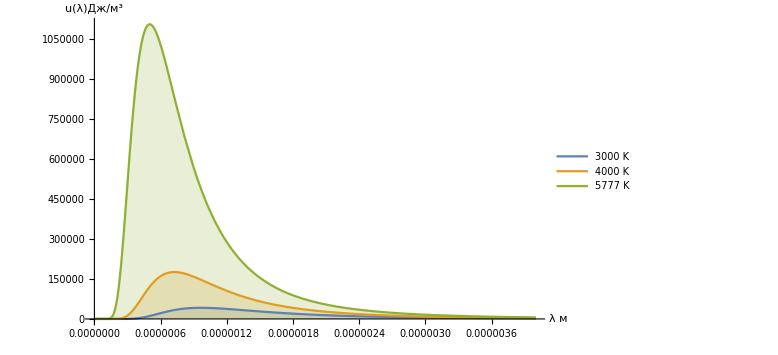

```mathematica
With[{Temp=Map[Quantity[#,"Kelvins"]&,{3000,4000,5777}]},
Quiet[Plot[Evaluate @ Map[plancksN[#,Quantity[λ,"Meters"]]&,Temp],{λ,0,4 10^-6},ImageSize->Large,Filling->Axis,PlotRange->All,PlotLegends->Temp,AxesLabel->{"λ м",Row[{"u(λ)",("Дж")/("м")^3}," "]}]]]
```

```mathematica
With[{Temp=Map[Quantity[#,"Kelvins"]&,{3000,4000,5777}]},
Quiet [ Plot[Evaluate @ Map[planckOmegaN[#,Quantity[ω,"Meters"]]&,Temp],{ω,0,9 10^15},
ImageSize->Large,
PlotRange->All,
PlotLegends->Temp,
AxesLabel->{"ω Гц",Row[{"u(ω)",("Дж")/("м")^3}," "]}]]]
```

-Graphics-

-Graphics-

```mathematica
planckOmega[T_,ω_]:=(ℏ ω^3)/(π^2 c^3)1/(Exp[(ℏ ω)/(k T)]-1);
jinsOmega[T_,ω_]:=k T ω^2/(π^2 c^3);
```

```mathematica
(*ℏ ω <<k T*)
```

```mathematica
planckOmega[T,ω]
```

(ω^3 ℏ)/(c^3 (-1+ⅇ^((ω ℏ)/(k T))) π^2)

```mathematica
%/.{ⅇ^x_->ⅇ^χ}
```

(ω^3 ℏ)/(c^3 (-1+ⅇ^χ) π^2)

```mathematica
%/.{ⅇ^χ->Series[Exp[χ],{χ,0,1}]}//Normal
```

(ω^3 ℏ)/(c^3 π^2 χ)

```mathematica
%/.{χ->(ω (ℏ/k))/T}
```

(k T ω^2)/(c^3 π^2)

```mathematica
%==jinsOmega[T,ω]
```

True

```mathematica
(*ℏ ω>>k T*)
```

```mathematica
vinOmega[T_,ω_,OptionsPattern[{C1->C1,C2->C2}]]:=
OptionValue[C1] ω^3 Exp[-OptionValue[C2] ω/T];
```

```mathematica
planckOmega[T,ω]
```

(ω^3 ℏ)/(c^3 (-1+ⅇ^((ω ℏ)/(k T))) π^2)

```mathematica
%/.{A_/(-1+ⅇ^χ_)->A/ⅇ^χ}
```

(ⅇ^(-(ω ℏ)/(k T)) ω^3 ℏ)/(c^3 π^2)

```mathematica
%==vinOmega[T,ω,C1-> 1/π^2 ℏ/c^3,C2-> ℏ/k]
```

True

-Graphics-

```mathematica
integralJins=Quiet[ Assuming[{ℏ>0,c>0,k>0,T>0},
∫_0^∞ jinsOmega[T,ω]ⅆω]]
```

∫_0^∞ (k T ω^2)/(c^3 π^2)ⅆω

```mathematica
integralVin=Assuming[{ℏ>0,c>0,k>0,T>0},
∫_0^∞ vinOmega[T,ω,C1-> 1/π^2 ℏ/c^3,C2-> ℏ/k]ⅆω]
```

(6 k^4 T^4)/(c^3 π^2 ℏ^3)

```mathematica
transfer[N [ UnitConvert[integralVin/.{T->Quantity[2000,"Kelvins"],c->cQ,ℏ->ℏQ,k->kQ}]]]
```

0.0111844 кг/(м с^2)

```mathematica
integralPlanck=Assuming[{ℏ>0,c>0,k>0,T>0},
∫_0^∞ planckOmega[T,ω]ⅆω]
```

(k^4 π^2 T^4)/(15 c^3 ℏ^3)

```mathematica
transfer [N [ UnitConvert[integralPlanck/.{T->Quantity[2000,"Kelvins"],c->cQ,ℏ->ℏQ,k->kQ}]]]
```

0.0121052 кг/(м с^2)

-Graphics-

```mathematica
integralForPlanck=Assuming[{ℏ>0,c>0,k>0,T>0},
∫_0^∞ ω planckOmega[T,ω]ⅆω]
```

(24 k^5 T^5 Zeta[5])/(c^3 π^2 ℏ^4)

```mathematica
transfer [N [ UnitConvert[%/.{T->Quantity[2000,"Kelvins"],k->kQ,c->cQ,ℏ->ℏQ}]]]
```

1.21467×10^13 кг/(м с^3)

-Graphics-

```mathematica
(*Нашел в задании 1.3*)
(* C1 -> 1/π^2 ℏ / c^3 , C2 ->  ℏ / k *)
```

-Graphics-

```mathematica
With[{f=vinOmega[T,#,C1-> 1/π^2 ℏ/c^3,C2-> ℏ/k]&},
Module[{ωLik,λLik},
ωLik=ω/.Solve[D[f[ω],ω]==0,ω,Reals][[2]];
Print [StringForm["Наиболее вероятная ω: `1` (`2` при T = 2000 К);",ωLik, transfer [N [ UnitConvert[ωLik/.{T->Quantity[2000,"Kelvins"],k->kQ,ℏ->ℏQ}]]]]];
λLik=With[{ν=2π ωLik},c/ν];
Print [StringForm["Наиболее вероятная λ: `1` (`2` при T = 2000 К).",λLik,transfer [ N [ UnitConvert[λLik/.{T->Quantity[2000,"Kelvins"],c->cQ,k->kQ,ℏ->ℏQ}]]]]];
]]
```

Наиболее вероятная ω: (3 k T)/ℏ (7.85522×10^14 1/с при T = 2000 К);

Наиболее вероятная λ: (c ℏ)/(6 k π T) (6.07411×10^-8 м при T = 2000 К).